# Fractional Derivatives

## Overview

### The Derivative Theorem

The theory of Fourier Transforms provides a wonderful relationship between a function and its derivative, roughly called the Derivative Theorem. Various properties of the Fourier Transform, include the Derivative Theorem, and their proofs can be fund here. In this notebook we want to see how this can be used to mathematically define a so-called fractional-derivative and examine some plots to gain intuition on what the mathematical operation does. What the physical interpretation of a fractional derivative might be is left for another time ...

### Notation

Let’s denote a function by f(x) and its Fourier Transform by F(ω). The Derivate Theorem states that the relationship between

## Define a function

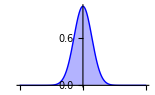

```mathematica
f[x_]:=Exp[-x^2];
Plot[f[x],{x,-5,5},PlotStyle->{Blue,Thick},PlotRange->All,Filling->Axis,FillingStyle->Lighter[Blue,0.7]]
```

## Calculate any order derivative analytically

In the cell below, the fractional derivative order is selected by the variable “fdOrder”. This can be changed and re-run.

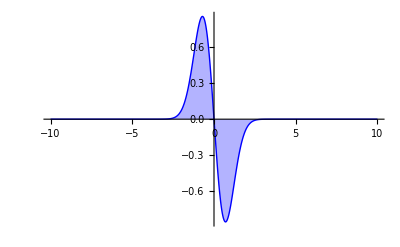

```mathematica
fdOrder=1;
ft=FourierTransform[f[x],x,w,FourierParameters->{0,-1}];
ift=InverseFourierTransform[(ⅈ w)^fdOrder ft,w,x,FourierParameters->{0,-1}];
Plot[ift,{x,-10,10},PlotStyle->{Blue,Thick},Filling->Axis,FillingStyle->Lighter[Blue,0.70],PlotRange->All]
```

## Plot 0-th, 1st, and 2nd derivative analytically

The 0th derivative is the original function itself, and the 1st and 2nd derivatives are the familiar derivatives we all know and love from physics, e.g. if the 0th derivative is a position function with respect to time then the 1st and 2nd derivatives are velocity and acceleration, respectively. The order of the derivative is given above each plot.

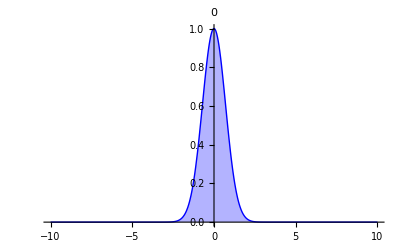
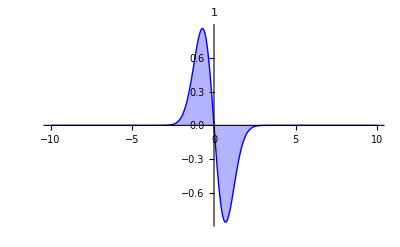
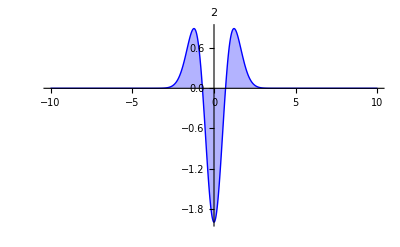

```mathematica
Table[
ft=FourierTransform[f[x],x,w,FourierParameters->{0,-1}];
ift=InverseFourierTransform[(ⅈ w)^fdOrder ft,w,x,FourierParameters->{0,-1}];
Plot[ift,{x,-10,10},PlotStyle->{Blue,Thick},Filling->Axis,FillingStyle->Lighter[Blue,0.70],PlotLabel->fdOrder,PlotRange->All],{fdOrder,0,2}
]
```

## Table Plot of Fractional Derivatives

Fractional derivatives from 0 to 2 in steps of 0.2. The order of the derivative is given above each plot.

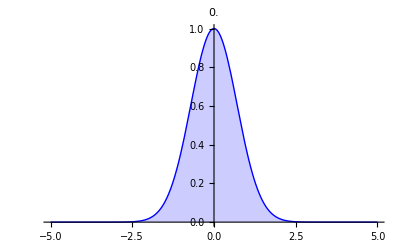
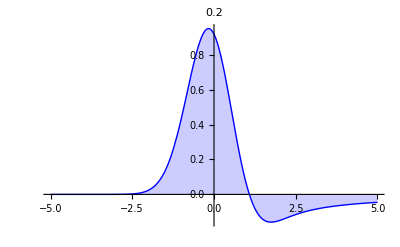
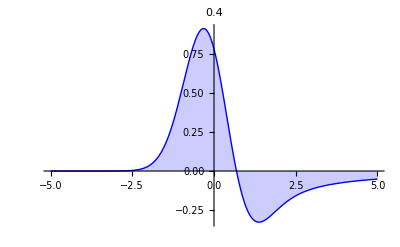
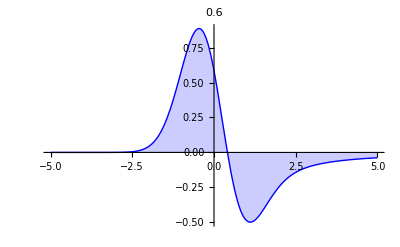
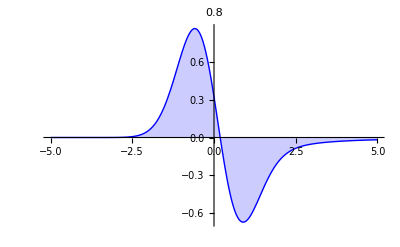
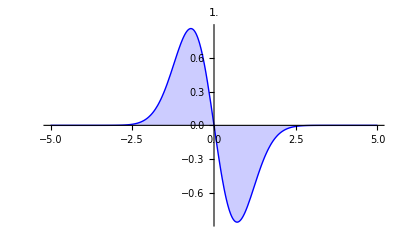
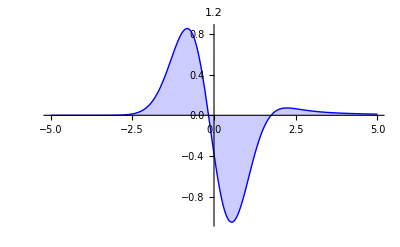
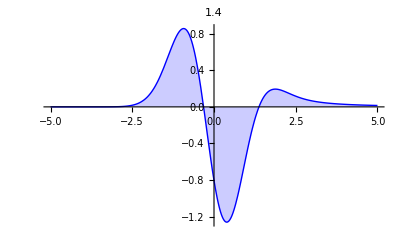

```mathematica
Table[
ift=InverseFourierTransform[(ⅈ w)^fdOrder ft,w,x,FourierParameters->{0,-1}];
Plot[ift,{x,-5,5},PlotRange->All,PlotStyle->{Blue,Thick},Filling->Axis,FillingStyle->Lighter[Blue,0.8],PlotLabel->fdOrder],
{fdOrder,0,2,0.2}]
```